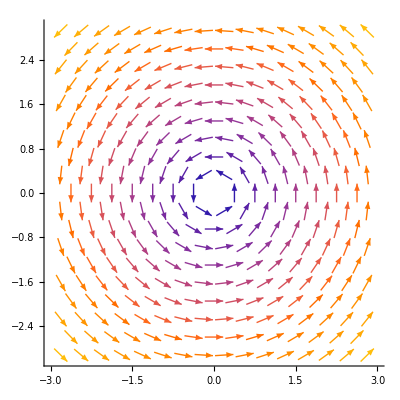

```mathematica
VectorPlot[{-y,x},{x,-3,3},{y,-3,3},Frame->False,Axes->True]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/test_vector_field.pdf",%2,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/test_vector_field.pdf

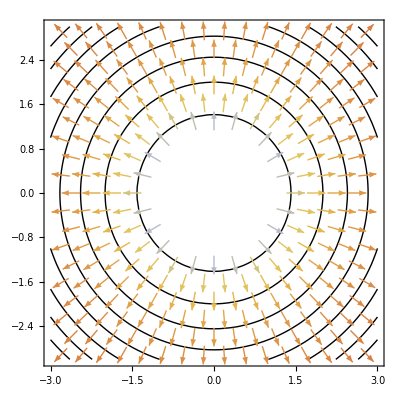

```mathematica
VectorPlot[{x,y}/(Norm[{x,y}]^3),{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->"BeachColors",VectorStyle->Gray];
Show[ContourPlot[(1/2)x^2 + (1/2)y^2,{x,-3,3},{y,-3,3},ContourShading->None],%]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/shells_vector_field_2.pdf",%59,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/shells_vector_field_2.pdf

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/shells_vector_field.pdf",%54,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/shells_vector_field.pdf

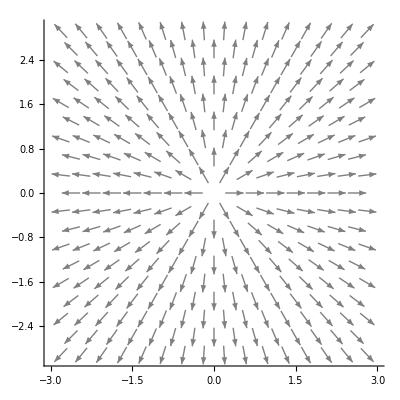

```mathematica
VectorPlot[{x,y},{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Gray]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/xyz_vector_field.pdf",%45,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/xyz_vector_field.pdf

```mathematica
StreamPlot[{x,y},{x,-3,3},{y,-3,3},Frame->False,Axes->True,StreamColorFunction->None,StreamStyle->Gray,StreamScale->None,StreamPoints->Coarse]
```

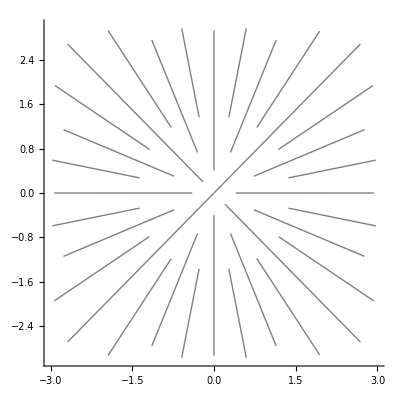

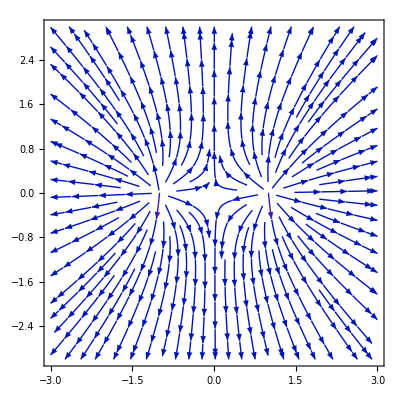

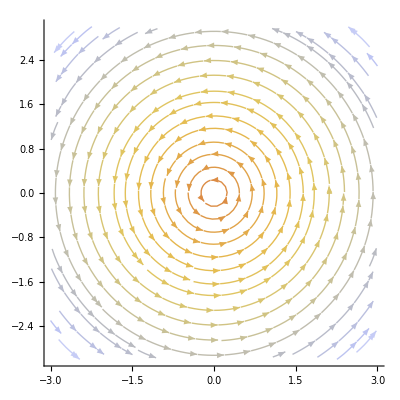

```mathematica
StreamPlot[{-y,x},{x,-3,3},{y,-3,3},StreamColorFunction->"BeachColors",Frame->False,Axes->True]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/phihat_field.pdf",%85,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/phihat_field.pdf

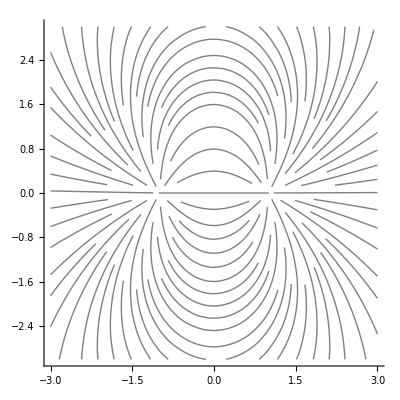

```mathematica
E1[x_,y_] = {x/(x^2 + y^2)^(1.5),y/(x^2 + y^2)^(1.5)};StreamPlot[E1[x+1,y] - E1[x-1,y],{x,-3,3},{y,-3,3},Frame->False,Axes->True,StreamScale->None,StreamColorFunction->None,StreamStyle->Gray]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/dipoles.pdf",%96,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/dipoles.pdf

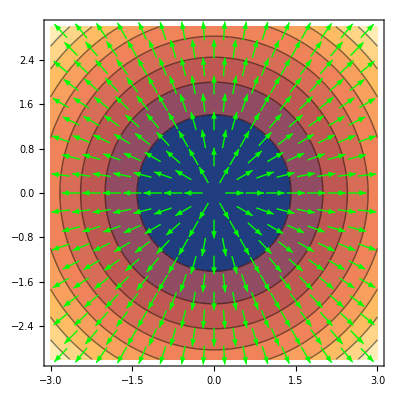

```mathematica
VectorPlot[{x,y},{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Green];
Show[ContourPlot[(1/2)x^2 + (1/2)y^2,{x,-3,3},{y,-3,3},ContourShading->Automatic],%]
```

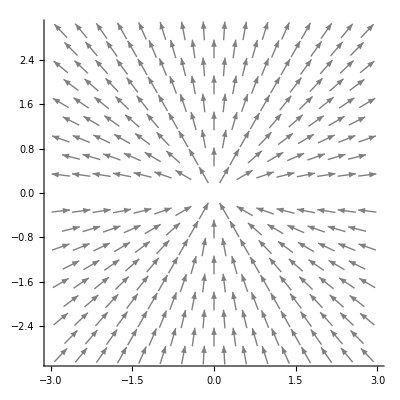

```mathematica
VectorPlot[{x*y,y^2},{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->{Red, Gray}]
```

```mathematica
A = {{1,2,3},{0,1,4},{0,0,-1}}
```

{{1,2,3},{0,1,4},{0,0,-1}}

```mathematica
A^2
```

{{1,4,9},{0,1,16},{0,0,1}}

```mathematica
MatrixPower[A,2]
```

{{1,4,8},{0,1,0},{0,0,1}}

```mathematica
MatrixPower[A,3]
```

{{1,6,11},{0,1,4},{0,0,-1}}

```mathematica
ResourceFunction["MatrixMinimalPolynomial"][A,x]
```

1-x+(-1+x) x^2

```mathematica
Simplify[%]
```

(-1+x)^2 (1+x)

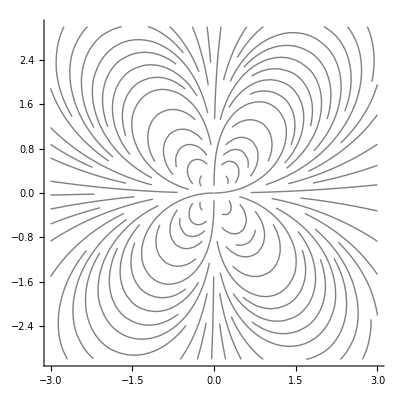

```mathematica
field={3/(4 r^4) (3 Cos[θ]^2-1),3/(4 r^4) Sin[2 θ]};
StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",field,{r,θ}->{x,y}],{x,-3,3},{y,-3,3},Frame->False,Axes->True,StreamColorFunction->None,StreamScale->None,StreamStyle->Gray]
```

```mathematica
field2 = {(r^2)Sin[Theta],0};
```

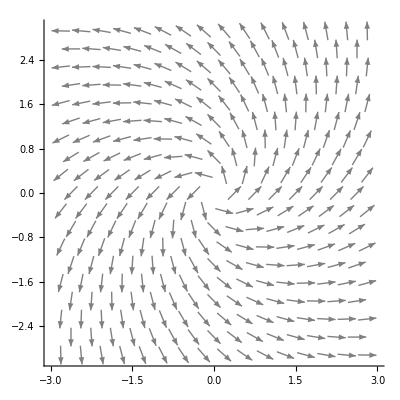

```mathematica
VectorPlot[{x-y,x+y},{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Gray]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/curl1a.pdf",%135,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/curl1a.pdf

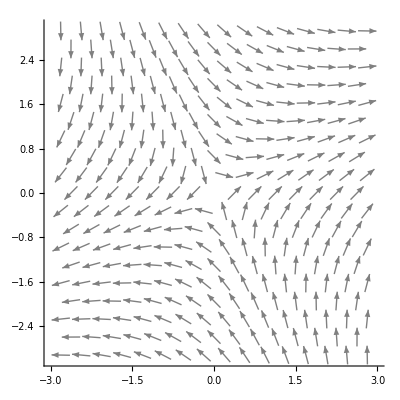

```mathematica
VectorPlot[{x+y,x-y},{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Gray]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/curl1b.pdf",%154,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/curl1b.pdf

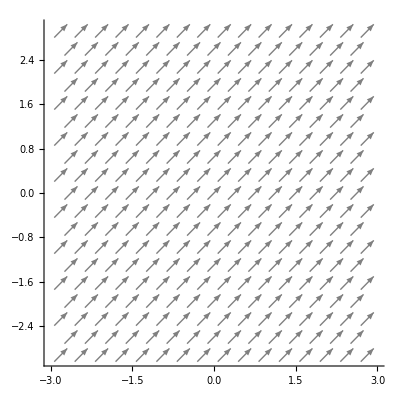

```mathematica
VectorPlot[{1,1},{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Gray]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/div0field.pdf",%155,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/div0field.pdf

```mathematica
VectorPlot[{x,y},{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Gray]
```

-Graphics-

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/spreadfield.pdf",%156,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Math Methods/images/spreadfield.pdf

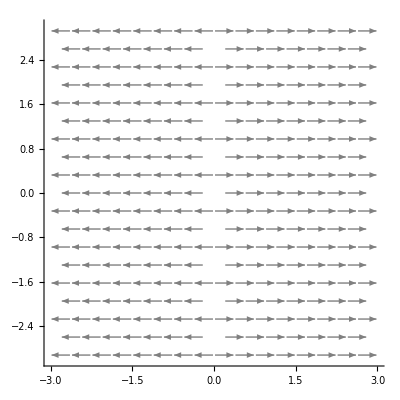

```mathematica
VectorPlot[{x,0},{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Gray]
```

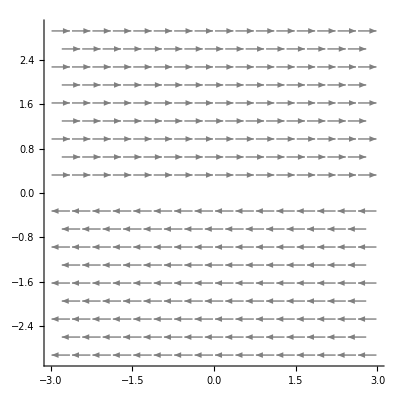

```mathematica
VectorPlot[{y,0},{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Gray]
```

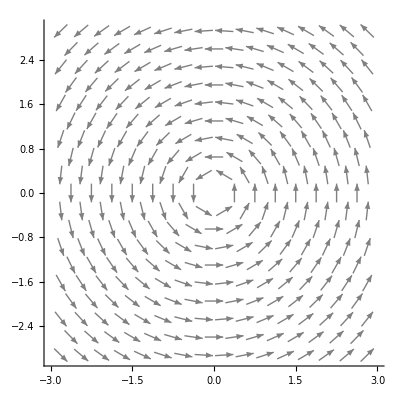

```mathematica
VectorPlot[Evaluate@TransformedField["Polar"->"Cartesian",{0,r},{r,θ}->{x,y}],{x,-3,3},{y,-3,3},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Gray]
```

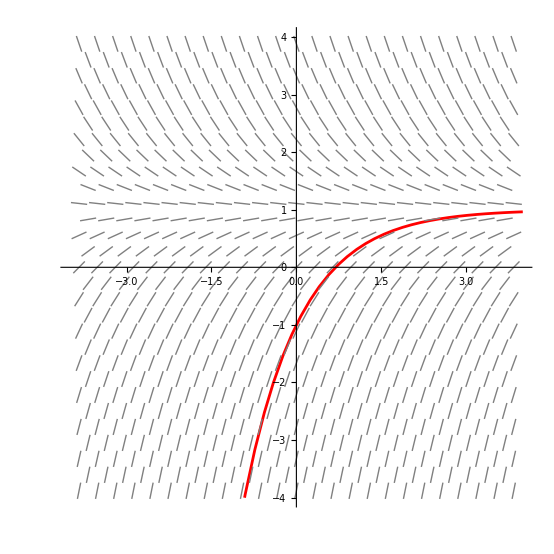

```mathematica
VectorPlot[{1,1-y},{x,-4,4},{y,-4,4},Frame->False,Ticks->None,VectorColorFunction->None,VectorStyle->Gray,VectorMarkers->"Segment",VectorPoints->Fine];
Show[Plot[1-2Exp[-x],{x,-4,4},PlotRange->{-4,4},PlotStyle->Red,AspectRatio->1],%]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/slopfieldwithexp.pdf",%184,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/slopfieldwithexp.pdf

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/slopfieldexp.pdf",%184,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/slopfieldexp.pdf

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/slopefieldexp.png",%184,"PNG"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/slopefieldexp.png

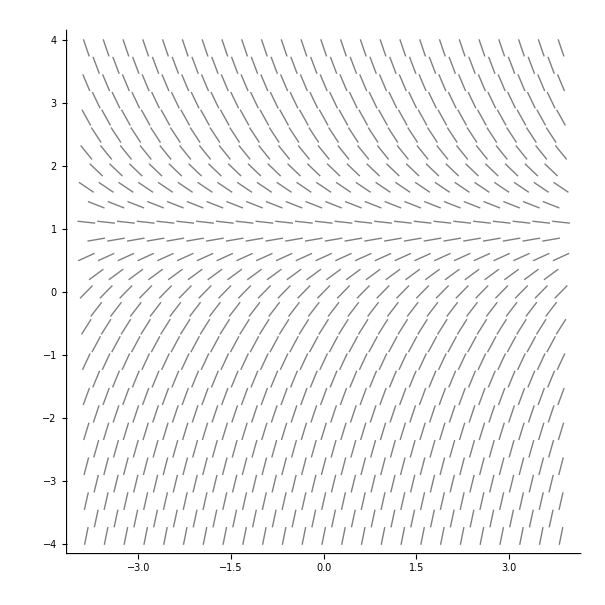

```mathematica
VectorPlot[{1,1-y},{x,-4,4},{y,-4,4},Frame->False,Axes->True,VectorColorFunction->None,VectorStyle->Gray,VectorMarkers->"Segment",VectorPoints->Fine]
```

```mathematica
Export["/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/slopefieldnoexp.pdf",%187,"PDF"]
```

/Users/avinashiyer/Documents/GitHub/ai-bearing.github.io/Classes_and_Homework/College/Y4/Y4S1, Ordinary Differential Equations/images/slopefieldnoexp.pdf

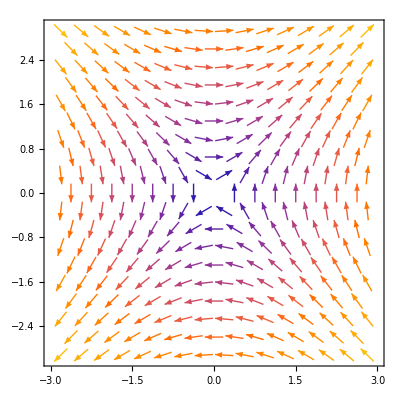

```mathematica
VectorPlot[{y,x},{x,-3,3},{y,-3,3}]
```

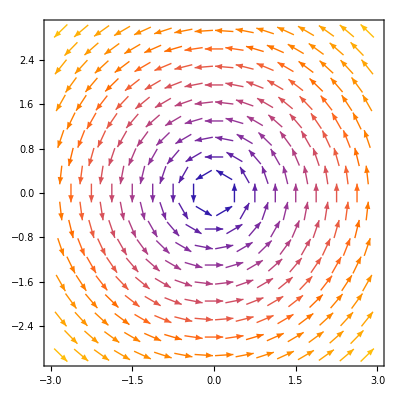

```mathematica
VectorPlot[{-y,x},{x,-3,3},{y,-3,3}]
```

```mathematica
Integrate[Sin[t]*(Cos[p]*Sin[t] + Sin[p]*Sin[t] + Cos[t]),{t,0,Pi/2},{p,0,2Pi}]
```

π